# Bloomberg Data to Mathematica

April 18, 2016

This code and the associated binaries, if properly installed, will allow you to load data from Bloomberg directly into Mathematica. It requires that you have a Bloomberg Professional license, have installed the Bloomberg API, and have logged in to Bloomberg Professional on the same machine as you’re running these functions on in the last 24 hours (and not logged in anywhere else more recently). This interface relies on DateObjects, TimeSeries and EventSeries, and will not work with versions of Mathematica earlier than 10.0. If you are using an old version of Mathematica, install the version of this interface titled “BBGetNF1-bloomberg into mathematica 201206”, which has many of the same capabilities and will run on much older versions of Mathematica.

To install, place the enclosed binaries into a folder (typically under “C:\Program Files\Wolfram Research\”, and by default “C:\Program Files\Wolfram Research\msFunctions\” though this can be changed with the “path to executable” option on each function.

This interface consists of four commands:

msBBGgetHistory: returns historical data from Bloomberg, normally in TemporalData format though alternatives are available. Can be used for example to retrieve U.S. CPI monthly back to 1969, or the closing price of Apple Inc. daily since 1978.
msGetBBG: Returns Bloomberg data for a single field for one or more securities. Works for both single-number reponses (such as current market cap) and multi-field responses (such as all registered owners). The FLDS command in Bloomberg can be used to identify what data is available for each security and which overrides, if any, are allowed.
msBBGetIntraday: returns intraday trade data (or ask data, or bid data)
msBBGetIntradayBars:  returns periodic intraday data (price snapshots every minute, for example).

The source code for these functions is available at
https://github.com/MichaelSternNYC/

## Code

```mathematica
bbgifyDate[date_]:=Module[{dtO},dtO=Which[StringQ[date]&&StringLength[date]==0,DateObject[],Head[date]===DateObject,date,True,DateObject[date]];DateString[dtO,{"Year","Month","Day"}]];(* converts date in any format to the string format bloomberg wants. If given empty string, returns today's date. *)

Options[msGetBBGMakeLinkObject]={"path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msGetBBGLink.exe"}]]};
msGetBBGMakeLinkObject[OptionsPattern[]]:=Install[OptionValue["path to executable"]];msGetBBGMakeLinkObject::usage = "msGetBBGMakeLinkObject[]: When run, launches the WSTP application that moves current data from Bloomberg to Mathematica. msGetBB[] will launch and kill this automatically, but you can do it manually with this function, assign the result to a variable, and pass the link to msGetBB[] with the \"LinkObject]\"→ option if you plan on calling it many times in succession.  This saves the overhead of relaunching the link for every call. When finished, can call Uninstall[(this link)] and the program will be quit. For most users it will be better to run msGetBBG[] with a list of tickers instead, as that approach returns data quicker (though tagged with each datum's ticker and potentially not in the same order those tickers were submitted to the function). Can set \"path to executable\" variable if the default is for some reason not what you want.";

Options[msGetBBG]={"noisy"->False,"outer noisy"->False,"LinkObject"->Null,"path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msGetBBGLink.exe"}]],"overrides"->{}};
msGetBBG[ticker_,field_String,OptionsPattern[]]:=Module[{raw,exp,link,ticks,trimmed,overrides},
link =If[Head[OptionValue["LinkObject"]]===LinkObject,OptionValue["LinkObject"],
 Install[OptionValue["path to executable"]]]; (* set up link to C++ Code if needed *)
ticks=If[StringQ[ticker],ticker,StringJoin[Riffle[ticker," & "]]];
If[OptionValue["outer noisy"]||OptionValue["outer noisy"],Print["ticks: ",ticks]];
overrides=If[Length[OptionValue["overrides"]]>0,StringJoin[Riffle[Riffle[Keys[OptionValue["overrides"]],Values[OptionValue["overrides"]]]," & "]],""];
If[OptionValue["outer noisy"],Print["overrides: ",overrides, ". (head: ",Head[overrides],")"]];
raw=msGetBBGLink[ticks,field,If[OptionValue["noisy"],1,0],overrides];
If[OptionValue["outer noisy"],Print["raw Head: ",Head[raw],". raw: ",raw]];
If[Head[OptionValue["LinkObject"]]===LinkObject,False,Uninstall[link]]; (* close link if needed *) 
If[Head[raw]===msGetBBGLink,Message[msGetBBG::linkDead];Null,(*else*)
If[!StringContainsQ[raw,"EXCEPTION"],
trimmed=StringTrim[raw];
If[OptionValue["outer noisy"],Print["trimmed: ",trimmed]];
exp=If[!OptionValue["noisy"],ToExpression[trimmed],trimmed];
If[Head[exp]===String,raw,exp],(* else, had exception *)
raw]
]
];
msGetBBG::usage = "msGetBBG[Bloomberg ticker_String OR _List,field_String,OptionsPattern[]]. Connects to Bloomberg and downloads a single field's data for one or more securities. Fields that return multiple lines (like dividend history or current holders) will be delivered as Lists of Associations. The user may wish to wrap each of these in a Dataset.

If you plan on running msGetBB[] many times in close succession, run msGetBBGMakeLinkObject[] first and save the resulting LinkObject to a variable. You can then pass that LinkObject to msGetBB[] with the \"LinkObject\"→ option, and Uninstall[] it when you are done. If you want to check multiple securities at once, pass them all to the function as a list (e.g. msGetBBG[{\"AAPL US Equity\",\"IBM US Equity\"},\"DVD_EX_DT\"]). For long lists this is about 20x faster than calling the function repeatedly. If used in this manner, the function may return the answers out of order, but will attach the security name to each datum for identification.

You can pass overrides to the function with \"overrides\"→<|\"field id 1\"→\"value 1\", \"field id 2\"→\"value two\", \"field id 3\"→\"field three\"|>}. Check the FLDS command for a security on the Bloomberg terminal to see which overrides are allowed. You can include an arbitrary number of overrides.

Can set the \"path to executable\" variable if the default is for some reason not what you want.
\"noisy\"→True will return debugging information from both the WSTP conduit and the Mathematica interface that calls it. \"outer noisy\"→True will debugging information from only the Mathematica part.";
msGetBBG::linkDead="Could not connect to link. Perhaps it died before Mathematica could pass data to it.";

Options[msBBGgetHistoryMakeLinkObject]={"path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msBBGgetHistoryLink.exe"}]]};
msBBGgetHistoryMakeLinkObject[OptionsPattern[]]:=Install[OptionValue["path to executable"]];msBBGgetHistoryMakeLinkObject::usage = "msBBGgetHistoryMakeLinkObject[]: When run, launches the WSTP application that moves historical securities data from Bloomberg to Mathematica. msBBGgetHistory[] will launch and kill this automatically, but you can do it manually with this function, assign the result to a variable, and pass the link to msBBGgetHistory[] with the \"LinkObject]\"→ option if you plan on calling it many times in succession.  This saves the overhead of relaunching the link for every call. When finished, can call Uninstall[(this link)] and the program will be quit. Can set \"path to executable\" variable if the default is for some reason not what you want.";

Options[msBBGgetHistory]={"adjust"->"CALENDAR","type"->"value","name"->"df","output"->"nf3"(* vs. "nf2" or "ts"*),"noisy"->False,"use DPDF"->False,"LinkObject"->Null,"path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","msBBGgetHistoryLink.exe"}]]};
msBBGgetHistory[ticker_String,field_String,start_,end_,freq_String,OptionsPattern[]]:= Module[{raw,name1,output,link, dateF,gotNada},
name1=If[OptionValue["name"]=="df",ticker<>": "<>field,OptionValue["name"]];
link =If[Head[OptionValue["LinkObject"]]===LinkObject,OptionValue["LinkObject"],
 Install[OptionValue["path to executable"]]]; (* set up link to C++ Code if needed *)
dateF=Switch[ToUpperCase[freq] ,"DAY","DAILY","WEEK","WEEKLY","MONTH","MONTHLY","QUARTER","QUARTERLY","YEAR","YEARLY","ANNUAL","YEARLY",_,ToUpperCase[freq]];
raw =msBBGgetHistoryLink[ticker, field,bbgifyDate[start],bbgifyDate[end],dateF,ToUpperCase[OptionValue["adjust"]],If[OptionValue["use DPDF"],1,0],If[OptionValue["noisy"],1,0]]; 
output=If[OptionValue["noisy"],raw,ToExpression[raw]];(* use ToExpression to convert C++ string output into list *)
(*If[OptionValue["noisy"],Print["raw: ",raw]];*)
If[Head[OptionValue["LinkObject"]]===LinkObject,False,Uninstall[link]]; (* close link if needed *) 
gotNada=If[Length[output]==0 && !OptionValue["noisy"],True,False];
Which[
!OptionValue["noisy"]&&!gotNada,output=Map[{Take[DateList[#[[1]]],3],#[[2]]}&,output];
output=Switch[OptionValue["type"],"value",TimeSeries[output],"pctchanges",EventSeries[output],"delta",EventSeries[output]];
output=Switch[OptionValue["output"],
"nf2",Association["name"->name1,"type"->OptionValue["type"],"data"->output],
"nf3",TemporalData[output,MetaInformation->{"name"->name1,"type"->OptionValue["type"]}],
"ts",output],
gotNada,Message[msBBGgetHistory::nodata,ticker];{},
!OptionValue["noisy"]&& StringLength[output]==0,output="Data not found. For more information, run with \"noisy\"→True",
OptionValue["noisy"],output
]
];
msBBGgetHistory::usage = 
"msBBGgetHistory[ticker_,field_,start_,end_,freq_,OptionsPattern[]] retrieves data from Bloomberg for a given ticker and field within the specified period.
PARAMETERS:
ticker: e.g., \"AAPL Equity\"
field: e.g., \"Px_Last\"
start: start date
end: end date, or \"\" for current day
freq: is the data frequency. Choices: \"day\", \"week\", \"month\", \"quarter\", or \"year\"\n

Optionally, you can pass  adjust→ for the period adjustment (default is \"CALENDAR\"). Choices, \"ACTUAL\", \"CALENDAR\"
type→ is one of \"delta\", \"pctchanges\", or (by default) \"value\". 
name→\"whatever\" sets the name.
\"output\"→\"nf2\", \"nf3\" (the new default) or \"ts\". nf2 is an association with Keys \"data\", \"name\" and \"type\". nf3 is a TemporalData object with the same information in MetaInformation. \"ts\" leaves out the MetaInformation.
\"noisy\"→(True or False), toggles debugging info
\"use DPDF\"→(True or False), toggles whether or not the DPDF settings in the Bloomberg terminal are respected. This would typically be used to shut off dividend adjustment, if it has been turned on.
\"LinkObject\" can be passed a link object created by msBBGgetHistoryMakeLinkObject[], saving the overhead of re-launching the link. If you do this, later Uninstall[] the link.
\"path to executable\"→should be set to the correct place by default but if you have more than one version of the executable, for example, you can pick one by setting the path here.

By default, pctchanges and delta-type data are stored as EventSeries[], while value-type data is stored as TimesSeries[]." ;
msBBGgetHistory::nodata="No data found for this time period for `1`."; 

Options[msBBGetIntradayMakeLinkObject]={"path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","BBRetrieveIntraday.exe"}]]};
msBBGetIntradayMakeLinkObject[OptionsPattern[]]:=Install[OptionValue["path to executable"]];msBBGetIntradayMakeLinkObject::usage = "msBBGetIntradayMakeLinkObject[]: When run, launches the WSTP application that moves historical intraday data from Bloomberg to Mathematica. msBBGetIntraday[] will launch and kill this automatically, but you can do it manually with this function, assign the result to a variable, and pass the link to msBBGetIntraday[] with the \"LinkObject]\"→ option if you plan on calling it many times in succession.  This saves the overhead of relaunching the link for every call. When finished, can call Uninstall[(this link)] and the program will be quit. Can set \"path to executable\" variable if the default is for some reason not what you want.";

Options[msBBGetIntraday]={"daylightsaving start"->{2015,3,8},"daylightsaving end"->{2015,11,1},"tick type"->"TRADE","LinkObject"->Null,"path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","BBRetrieveIntraday.exe"}]],"output"->Association(*or List*)};msBBGetIntraday[ticker_String,starttime_DateObject,endtime_DateObject,OptionsPattern[]]:=Module[{output, link,st,et,daylighttimezone,dateformat,x,fld,ok}, ok=True;
If[MemberQ[{"trade","bid","ask"},ToLowerCase[OptionValue["tick type"]]],fld=ToUpperCase[OptionValue["tick type"]],ok=False];
link =If[Head[OptionValue["LinkObject"]]===LinkObject,OptionValue["LinkObject"],
 Install[OptionValue["path to executable"]]]; (* set up link to C++ Code if needed *)
daylighttimezone = -4;
dateformat = {"Year","-","Month","-","Day","T","Time"};
st = AbsoluteTime[starttime];
st=If[AbsoluteTime[OptionValue["daylightsaving start"]]≤st&&AbsoluteTime[OptionValue["daylightsaving end"]]≥ st,DateString[DateList[DatePlus[st,{-daylighttimezone,"Hour"}]],dateformat],DateString[DateList[DatePlus[st,{-(daylighttimezone-1),"Hour"}]],dateformat]];
et = AbsoluteTime[endtime];
et=If[AbsoluteTime[OptionValue["daylightsaving start"]]≤et&&AbsoluteTime[OptionValue["daylightsaving end"]]≥ et,DateString[DateList[DatePlus[et,{-daylighttimezone,"Hour"}]],dateformat],DateString[DateList[DatePlus[et,{-(daylighttimezone-1),"Hour"}]],dateformat]]; 
x=BBRetrieveIntraday[ticker,fld,st,et];
output = ToExpression[x];(*using ToExpression to convert C++ string output into list *)
output=Map[{AbsoluteTime[{StringDrop[#[[1]],-10],dateformat}],#[[2]],#[[3]]}&,output];
output = Map[{If[AbsoluteTime[OptionValue["daylightsaving start"]]≤#[[1]]&& AbsoluteTime[OptionValue["daylightsaving end"]]≥ #[[1]],DateObject[DateList[DatePlus[#[[1]],{daylighttimezone,"Hour"}]]],DateObject[DateList[DatePlus[#[[1]],{daylighttimezone-1,"Hour"}]]]],#[[2]],#[[3]]}&,output];
output = If[OptionValue["output"]===List,output,Map[<|"Time"->#[[1]],"Price"->#[[2]],"Size"->#[[3]]|>&,output]];
If[Head[OptionValue["LinkObject"]]===LinkObject,False,Uninstall[link]]; (* close link if needed *) 
 output]

msBBGetIntraday::usage = 
"msBBGetIntraday[ticker_,starttime_,endtime_] retrieves intraday ticks from Bloomberg for a given ticker within the specified period. 
PARAMETERS:
ticker: e.g., \"AAPL Equity\"
starttime: DateObject indicating start date and time
endtime: DateObject indicating end date and time.

Bloomberg seems to save detailed intraday data back six months.

By default returns trade data, but can set option \"tick type\" to \"BID\" or \"ASK\" if you want something different.

Returns a three-member list for every datapoint available: {time, price, size}. Pass \"output\"→Association if you prefer an Association to the list. Oother optional parameters include \"daylightsaving beg\" and \"daylightsaving end\", which change every year. For a liquid security, the number of datapoints here is likely to be enormous, and you may want to consider using msBBGetIntradayBars[] instead.

\"LinkObject\" can be passed a link object created by msBBGetIntradayMakeLinkObject[], saving the overhead of re-launching the link. If you do this, later Uninstall[] the link.
\"path to executable\"→should be set to the correct place by default but if you have more than one version of the executable, for example, you can pick one by setting the path here.";

Options[msBBGetIntradayBarsMakeLinkObject]={"path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","BBRetrieveIntradayBars.exe"}]]};
msBBGetIntradayBarsMakeLinkObject[OptionsPattern[]]:=Install[OptionValue["path to executable"]];msBBGetIntradayBarsMakeLinkObject::usage = "msBBGetIntradayBarsMakeLinkObject[]: When run, launches the WSTP application that moves historical intraday bar data from Bloomberg to Mathematica. msBBGetIntradayBars[] will launch and kill this automatically, but you can do it manually with this function, assign the result to a variable, and pass the link to msBBGetIntradayBars[] with the \"LinkObject]\"→ option if you plan on calling it many times in succession.  This saves the overhead of relaunching the link for every call. When finished, can call Uninstall[(this link)] and the program will be quit. Can set \"path to executable\" variable if the default is for some reason not what you want.";

Options[msBBGetIntradayBars]={"daylightsaving start"->{2015,3,8},"daylightsaving end"->{2015,11,1},"fill"->1,"tick type"->"TRADE","path to executable"->FileNameJoin[Flatten[{Drop[FileNameSplit[$InstallationDirectory],-2],"msFunctions","BBRetrieveIntradayBars.exe"}]],"LinkObject"->Null,"output"->Association(*or List*)};msBBGetIntradayBars[ticker_String,starttime_DateObject,endtime_DateObject,barsize_/;NumberQ[barsize],OptionsPattern[]]:=Module[{output, link,st,et,x,daylighttimezone,dateformat,fld,ok,dsb,dse},
 ok=True;
If[MemberQ[{"trade","bid","ask"},ToLowerCase[OptionValue["tick type"]]],fld=ToUpperCase[OptionValue["tick type"]],ok=False];
link =If[Head[OptionValue["LinkObject"]]===LinkObject,OptionValue["LinkObject"],
 Install[OptionValue["path to executable"]]]; (* set up link to C++ Code if needed *)
 dsb = AbsoluteTime[OptionValue["daylightsaving start"]]; (*Remember to reset this every year*)
dse = AbsoluteTime[OptionValue["daylightsaving end"]];(*Remember to reset this every year*)
daylighttimezone = -4;
dateformat = {"Year","-","Month","-","Day","T","Time"};
st = AbsoluteTime[starttime];
st=If[dsb≤st&&dse≥ st,DateString[DateList[DatePlus[st,{-daylighttimezone,"Hour"}]],dateformat],DateString[DateList[DatePlus[st,{-(daylighttimezone-1),"Hour"}]],dateformat]];
et = AbsoluteTime[endtime];
et=If[dsb≤et&&dse≥ et,DateString[DateList[DatePlus[et,{-daylighttimezone,"Hour"}]],dateformat],DateString[DateList[DatePlus[et,{-(daylighttimezone-1),"Hour"}]],dateformat]]; 
x=BBRetrieveIntradayBars[ticker,fld,st,et,barsize,OptionValue["fill"]];
output = ToExpression[x];(*using ToExpression to convert C++ string output into list *)
output = Map[{If[dsb≤AbsoluteTime[{StringDrop[#[[1]],-10],dateformat}]&& dse≥ AbsoluteTime[{StringDrop[#[[1]],-10],dateformat}],DateObject[DateList[DatePlus[AbsoluteTime[StringDrop[#[[1]],-10]],{daylighttimezone,"Hour"}]]],DateObject[DateList[DatePlus[AbsoluteTime[StringDrop[#[[1]],-10]],{daylighttimezone-1,"Hour"}]]]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]],#[[7]]}&,output];
output = If[OptionValue["output"]===List,output,Map[<|"Time"->#[[1]],"Open"->#[[2]],"High"->#[[3]],"Low"->#[[4]],"Close"->#[[5]],"Tick Counts"->#[[6]],"Shares"->#[[7]]|>&,output]];
If[Head[OptionValue["LinkObject"]]===LinkObject,False,Uninstall[link]]; (* close link if needed *) 
 output]

msBBGetIntradayBars::usage = 
"msBBGetIntradayBars[ticker_,starttime_,endtime_,barsize_] retrieves intraday samples from Bloomberg for a given ticker within the specified period. 
PARAMETERS:
ticker: e.g., \"AAPL Equity\"
starttime: DateObject indicating start date and time
endtime: DateObject indicating end date and time
barsize: is the sample frequency, in minutes
Optionally, can pass
	\"tick type\" →  \"TRADE\" or \"BID\" or \"ASK\", and/or
	\"fill\"→ If this is set to 1, the API will append previous day close information as first datapoint as the start of trading for the specified period. Otherwise, the first data point will be the actual first trading on that day.

Bloomberg seems to save detailed intraday data back six months.

Returns seven items for each bar —
1: Time
2: Open
3: High
4: Low
5: Close
6: Tick Counts per bar
7: Shares per bar

By default returns these in List format, but pass \"output\"→Association if you prefer it that way.
\"LinkObject\" can be passed a link object created by msBBGetIntradayBarsMakeLinkObject[], saving the overhead of re-launching the link. If you do this, later Uninstall[] the link.
\"path to executable\"→should be set to the correct place by default but if you have more than one version of the executable, for example, you can pick one by setting the path here.

If you want every trade, rather than periodic samples, use msBBGetIntraday[].";
```

## Examples

Get one datapoint

```mathematica
msGetBBG["C US Equity","PX_LAST"]
```

43.745

Get multiple datapoint -- if you ask for a lot of names, Bloomberg may not return the answers in order, so the WSTP interface tags each answer with the corresponding security name.

```mathematica
msGetBBG[{"IBM US Equity","AAPL US Equity"},"PX_LAST"]
```

{{IBM US Equity,145.6},{AAPL US Equity,105.67}}

Works with text as well as numbers.

```mathematica
msGetBBG["IBM US Equity","General_Counsel"]
```

"MICHELLE H BROWDY"

Works with arrays of data (which are often most conveniently stored as Datasets), and handles missing fields elegantly.

```mathematica
Dataset[msGetBBG["CAR US Equity","DVD_HIST_ALL"]]
```

Declared Date | Ex-Date | Record Date | Payable Date | Dividend Amount | Dividend Frequency | Dividend Type
2006-08-23 | 2006-09-05 | 2006-09-05 | KeyAbsent | 0.1 | None | Stock Split
2005-10-24 | 2006-08-01 | 2006-07-21 | 2006-07-31 | 0.2 | None | Spinoff
2005-10-24 | 2006-08-01 | 2006-07-21 | 2006-07-31 | 0.25 | None | Spinoff
2006-07-13 | 2006-07-21 | 2006-07-21 | KeyAbsent | 1. | None | Poison Pill Rights
2006-05-19 | 2006-05-19 | KeyAbsent | KeyAbsent | KeyAbsent | Suspend | Discontinued
2006-02-09 | 2006-02-23 | 2006-02-27 | 2006-03-14 | 1.1 | Quarter | Regular Cash
2005-10-18 | 2005-11-17 | 2005-11-21 | 2005-12-13 | 1.1 | Quarter | Regular Cash
2005-07-19 | 2005-08-18 | 2005-08-22 | 2005-09-13 | 1.1 | Quarter | Regular Cash
2005-04-26 | 2005-05-19 | 2005-05-23 | 2005-06-14 | 0.9 | Quarter | Regular Cash
2005-01-24 | 2005-02-24 | 2005-02-28 | 2005-03-15 | 0.9 | Quarter | Regular Cash
2004-10-12 | 2005-02-01 | 2005-01-19 | 2005-01-31 | 0.05 | None | Spinoff
2004-10-19 | 2004-11-18 | 2004-11-22 | 2004-12-14 | 0.9 | Quarter | Regular Cash
2004-07-20 | 2004-08-12 | 2004-08-16 | 2004-09-14 | 0.9 | Quarter | Regular Cash
2004-04-20 | 2004-05-20 | 2004-05-24 | 2004-06-15 | 0.7 | Quarter | Regular Cash
2004-02-11 | 2004-02-19 | 2004-02-23 | 2004-03-16 | 0.7 | Quarter | Regular Cash
1996-09-25 | 1996-10-22 | 1996-10-07 | 1996-10-21 | 1.5 | None | Stock Split
⋮_5 |  |  |  |  |  | 
2 levels | 21rows |  |  |  |  |  | Dataset[{__Association}]

Historical data is by default returned as TemporalData[]

```mathematica
histExample=msBBGgetHistory["AAPL Equity","Px_Last",DateObject["20070901"],DateObject["20081020"],"month"]
```

TemporalData[…]

msBBGgetHistory records type and name in this TemporalData as Metadata, so it can be easily retrieved thusly:

```mathematica
histExample["name"]
```

AAPL Equity: Px_Last

You can tap the Bloomberg output with

Historical intraday data comes from separate functions:

```mathematica
x=msBBGetIntraday["SPX Index",DateObject["2014-12-03T09:30:00"],DateObject["2014-12-03T09:31:00"]]
```

{{Wed 3 Dec 2014 09:30:01,2067.45,0},{Wed 3 Dec 2014 09:30:06,2067.62,0},{Wed 3 Dec 2014 09:30:11,2067.59,0},{Wed 3 Dec 2014 09:30:16,2067.45,0},{Wed 3 Dec 2014 09:30:21,2067.74,0},{Wed 3 Dec 2014 09:30:26,2067.82,0},{Wed 3 Dec 2014 09:30:31,2067.79,0},{Wed 3 Dec 2014 09:30:36,2067.93,0},{Wed 3 Dec 2014 09:30:41,2068.15,0},{Wed 3 Dec 2014 09:30:46,2068.38,0},{Wed 3 Dec 2014 09:30:51,2068.39,0},{Wed 3 Dec 2014 09:30:56,2068.37,0}}

```mathematica
x=msBBGetIntradayBars["INDU Index",DateObject["2014-12-02T09:30:00"],DateObject["2014-12-02T10:30:00"],10]
```

{{Tue 2 Dec 2014 09:30:00,17778.9,17826.8,17778.9,17820.,300,0},{Tue 2 Dec 2014 09:40:00,17819.4,17824.5,17801.9,17805.5,300,0},{Tue 2 Dec 2014 09:50:00,17806.4,17817.8,17797.6,17811.8,300,0},{Tue 2 Dec 2014 10:00:00,17813.,17844.3,17813.,17836.5,300,0},{Tue 2 Dec 2014 10:10:00,17836.2,17838.1,17829.7,17837.6,300,0},{Tue 2 Dec 2014 10:20:00,17837.4,17840.9,17832.5,17833.2,300,0}}

If you will be calling these functions repeatedly, it makes sense to leave the link live and save the time of relaunching it.

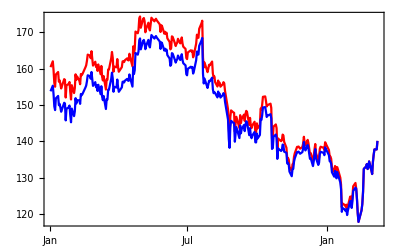

```mathematica
histLink=msBBGgetHistoryMakeLinkObject[];
x1=msBBGgetHistory["IBM US Equity","Px_Close_1D",{2015,1,1},"","Day","use DPDF"->False,LinkObject->histLink];
x2=msBBGgetHistory["IBM US Equity","Px_Close_1D",{2015,1,1},"","Day","use DPDF"->True,LinkObject->histLink];
DateListPlot[{x1,x2},PlotStyle->{Red,Blue}]
```

```mathematica
Uninstall[histLink]
```

"C:\Program Files\Wolfram Research\msFunctions\msBBGgetHistoryLink.exe"

With overrides,

```mathematica
msGetBBG["AAPL US Equity","BETA_RAW_OVERRIDABLE","noisy"->False,"overrides"-><|"BETA_OVERRIDE_REL_INDEX"->"NDX Index", "BETA_OVERRIDE_START_DT"->bbgifyDate[{2015,2,3}], "BETA_OVERRIDE_END_DT"->bbgifyDate[{2015,12,3}]|>]
```

1.20632